```mathematica
data=Import["~/Documents/wiwiwi/semestr_2/aisd/4_powracanie/input/200_30", "Table"];
```

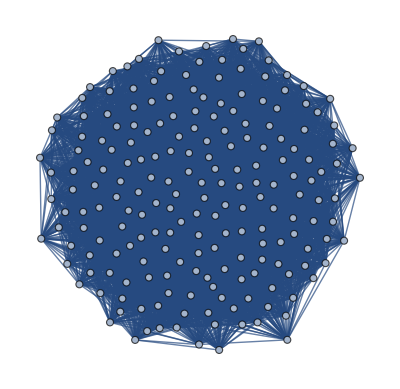

```mathematica
g=AdjacencyGraph[data]
```

```mathematica
HamiltonianGraphQ[g]
EulerianGraphQ[g]
ConnectedGraphQ[g]
```

True

True

True

```mathematica
hc=FindHamiltonianCycle[g,4000];
ec=FindEulerianCycle[g];
```

```mathematica
NormCycle[cycle_]:=(First/@cycle)-1
```

```mathematica
First@ec//NormCycle//Reverse;
```